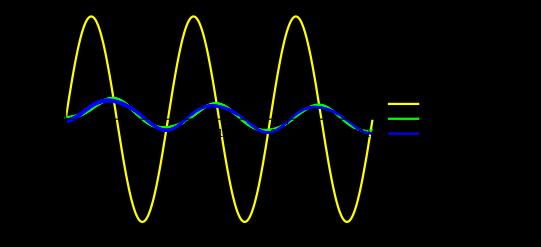

```mathematica
ClearAll["Global*`"];

(* součástky *)
R1 = 10 * 10^3;
R2 = 22 * 10^3;
R3 = 33 * 10^3;

C1 = 56 * 10^-9;
C2 = 47 * 10^-9;
L = 82 * 10^-6;

amplitudaU = 5;
frekvenceU = 1200;

amplitudaI = 100 * 10^-3;
frekvenceI = 2400;

tmax = 3 / frekvenceU;

(* rovnice uzlů a součástek, počáteční podmínky *)

uz[t_] := amplitudaU*(Sin[2*Pi*frekvenceU*t])/2;
iz[t_] := amplitudaI*(Sin[2*Pi*frekvenceI*t])/2;

rovnice = {
0 == iU[t] + iR1[t],
iR1[t] + iz[t] == iR2[t] + iC1[t] + iL[t],
iL[t] == iz[t] + iR3[t] + iC2[t],

u1[t] == uz[t],
u1[t] - u2[t] == R1 * iR1[t],
u2[t] == R2 * iR2[t],
u3[t] == R3 * iR3[t],
u2[t] - u3[t] == L * iL'[t],

iC1[t] == C1 * u2'[t],
iC2[t] == C2 * u3'[t],

iL[0] == 0,
u2[0] == 0,
u3[0] == 0
};

nezname = Union[Cases[rovnice, _Symbol[t], {0, Infinity}]];
reseni = NDSolve[rovnice, nezname, {t, 0, tmax}, StartingStepSize-> 10^-9];

(* Vykreslení grafu - pozor na parametry *)
Plot[{u1[t] /. reseni[[1]], u2[t] /. reseni[[1]], u3[t] /. reseni[[1]]}, {t, 0, tmax}, PlotStyle -> {Yellow, Green, Blue}, PlotLegends -> {"u1(t)", "u2(t)", "u3(t)"}, Background -> Black, PlotRange -> Full]
```